## Notas

Todas las matrices se pueden precomputar y sólo variar

```mathematica
HxMatrix[hx_,L_,base_]:=HxMatrix[hx,L,base]=Module[{dimSubspace=Length[base],q,l,tmp1,m},m=SparseArray[Prepend[Table[tmp1=Select[Join[ConstantArray[j,L]-IdentityMatrix[L],If[PalindromeQ[j],{},ConstantArray[Reverse[j],L]-IdentityMatrix[L]]],And@@NonNegative[#]&];
q=Boole@Not@PalindromeQ[j];
Total[Table[l=Boole@Not@PalindromeQ[k];
pos=Flatten@Position[base,If[MemberQ[base,k],k,Reverse[k]]];
SparseArray[pos->2^(-(q+l)/2),dimSubspace],{k,tmp1}]],{j,base[[2;;]]}],SparseArray[{},dimSubspace]];
hx*(Transpose[m]+m)]]
```

```mathematica
Hx[hx_,L_,base_]:=Hx[hx,L,base]=
Module[{dimSubspace=Length[base],q,l,tmp1,m},
m=SparseArray[
Prepend[
Table[
tmp1=Select[Join[ConstantArray[j,L]-IdentityMatrix[L],If[PalindromeQ[j],{},ConstantArray[Reverse[j],L]-IdentityMatrix[L]]],And@@NonNegative[#]&];
q=ReplaceAll[PalindromeQ[j],{True->0,False->1}];
Total[
Table[
l=ReplaceAll[PalindromeQ[k],{True->0,False->1}];
SparseArray[Flatten[Position[base,If[MemberQ[base,k],k,Reverse[k]]]]->2^(-(q+l)/2),dimSubspace]
,{k,tmp1}]
]
,{j,base[[2;;]]}]
,SparseArray[{},dimSubspace]
]
];

hx*(Transpose[m]+m)+hz*DiagonalMatrix[Total[(-1)^#]&/@base,TargetStructure->"Sparse"]-J*DiagonalMatrix[Total[(-1)^Differences[#]]&/@base,TargetStructure->"Sparse"]
]
```

```mathematica
Hx[1.,11,base]
```

SparseArray[…]

```mathematica
Hx[2.,11,base]
```

$Aborted

## Memoization

## Definiciones

```mathematica
PositiveParitySubspaceBasis[L_]:=DeleteDuplicatesBy[Tuples[{0,1},L],First[Sort[{#,Reverse[#]}]]&];
```

```mathematica
L=11;
base=PositiveParitySubspaceBasis[L];

(*Esto seguro se puede optimizar, pero queda para después*)
Hx=Module[{m,dimSubspace=Length[base]},
m=SparseArray[Prepend[
Table[
tmp1=Select[Join[ConstantArray[j,L]-IdentityMatrix[L],If[PalindromeQ[j],{},ConstantArray[Reverse[j],L]-IdentityMatrix[L]]],And@@NonNegative[#]&];
q=ReplaceAll[PalindromeQ[j],{True->0,False->1}];
Total[
Table[
l=ReplaceAll[PalindromeQ[k],{True->0,False->1}];
SparseArray[Flatten[Position[base,If[MemberQ[base,k],k,Reverse[k]]]]->2^(-(q+l)/2),dimSubspace]
,{k,tmp1}]
]
,{j,base[[2;;]]}]
,SparseArray[{},dimSubspace]
]];
ConjugateTranspose[m]+m
]
```

SparseArray[…]

```mathematica
Hz=DiagonalMatrix[Total[(-1)^#]&/@base,TargetStructure->"Sparse"]
```

SparseArray[…]

```mathematica
JJ=DiagonalMatrix[Total[(-1)^Differences[#]]&/@base,TargetStructure->"Sparse"]
```

SparseArray[…]

```mathematica
Hamiltonian[hx_,hz_,J_]:=hx*Hx+hz*Hz-J*JJ
```

```mathematica
Hamiltonian[hx_,hz_,J_,L_,base_]:=Module[{dimSubspace=Length[base],q,l,tmp1,m},
(* sum of sigmaX *)
m=
SparseArray[Prepend[
Table[
tmp1=Select[Join[ConstantArray[j,L]-IdentityMatrix[L],If[PalindromeQ[j],{},ConstantArray[Reverse[j],L]-IdentityMatrix[L]]],And@@NonNegative[#]&];
q=ReplaceAll[PalindromeQ[j],{True->0,False->1}];
Total[
Table[
l=ReplaceAll[PalindromeQ[k],{True->0,False->1}];
SparseArray[Flatten[Position[base,If[MemberQ[base,k],k,Reverse[k]]]]->2^(-(q+l)/2),dimSubspace]
,{k,tmp1}]
]
,{j,base[[2;;]]}]
,SparseArray[{},dimSubspace]
]];

hx*(Transpose[m]+m)+hz*DiagonalMatrix[Total[(-1)^#]&/@base,TargetStructure->"Sparse"]-J*DiagonalMatrix[Total[(-1)^Differences[#]]&/@base,TargetStructure->"Sparse"]
]
```

```mathematica
hx=1.;
hz=2.9;
J=1.2;
L=11;base=PositiveParitySubspaceBasis[L];
AbsoluteTiming[H=Hamiltonian[hx,hz,J,L,base]]
```

{8.14299,SparseArray[…]}

```mathematica
AbsoluteTiming[Eigenvalues[Normal[H]]]
```

{0.068351,{-44.9874,-36.6234,-34.4933,-34.4579,-34.3711,-34.273,-34.2087,-30.4139,-28.3027,-28.2595,-28.2221,-28.2185,-28.2139,-26.2937,-26.1256,-26.099,-26.052,-25.9939,-25.9343,-25.883,-25.8482,24.9809,-24.1256,-24.093,-24.069,-24.0457,-23.9792,-23.9624,-23.915,-23.8724,-23.811,-23.7926,-23.7563,-23.7019,-23.6945,-23.6891,-23.5977,-23.5711,-23.4776,22.9953,22.7553,22.3729,-22.0499,22.028,21.8735,-21.8313,-21.746,-21.7453,-21.7444,20.8879,20.7121,20.6164,20.5334,-20.4345,20.2528,20.2119,20.1416,19.9985,-19.9388,-19.9155,-19.8848,19.8794,-19.8593,-19.8572,-19.8543,-19.8511,-19.8488,19.834,-19.831,19.8103,-19.7699,-19.7174,-19.6754,-19.6403,19.5948,19.4596,19.3631,19.1565,19.0399,18.8453,18.7224,18.6145,18.5499,18.4479,-18.299,18.2363,-18.2288,-18.2276,18.151,18.1292,17.9997,-17.9299,17.883,17.8048,-17.8024,17.7991,-17.7597,-17.7426,17.7366,-17.7159,-17.7083,-17.6968,-17.6896,17.6876,17.6783,-17.6688,-17.6451,-17.6207,-17.6146,-17.6101,17.6089,-17.5807,-17.5609,-17.5599,-17.5546,-17.5293,-17.4946,-17.4901,-17.4838,17.465,-17.4506,-17.4439,17.4162,17.3372,17.3119,17.2751,17.0407,16.9761,16.9515,16.8311,16.5931,16.5233,16.4546,16.4435,16.4059,16.366,16.2786,16.2393,16.2133,16.1786,16.1766,16.0467,16.0357,-15.9902,15.9449,15.858,15.8492,-15.8403,15.8201,-15.7956,15.765,-15.7643,-15.7616,15.7357,-15.7232,-15.7064,-15.7031,-15.6855,-15.6371,15.6182,-15.5984,15.5844,-15.5724,-15.5592,-15.5244,15.5019,15.4822,-15.4815,-15.4547,-15.4285,-15.4075,15.3863,-15.3697,-15.3687,15.3681,-15.3549,-15.354,15.3013,-15.3011,15.2778,-15.2768,-15.2226,-15.1454,15.1219,15.0471,15.0227,15.0003,14.8732,14.8656,14.7732,14.6086,14.4487,14.4397,14.4311,14.4012,14.3572,14.1987,-14.193,14.1921,14.1882,14.1587,14.134,14.1277,14.08,13.9709,13.9438,13.9407,13.9141,13.8955,-13.8214,13.804,-13.7741,-13.7662,13.7375,13.7337,-13.7292,13.7014,-13.6711,-13.6493,-13.6468,-13.643,-13.6396,13.6333,13.6253,-13.624,13.6051,13.596,-13.5815,-13.565,13.545,-13.5206,-13.4866,-13.4673,13.4653,-13.4617,13.4578,-13.4563,-13.4179,-13.4123,13.3951,-13.3854,-13.382,-13.3812,-13.3806,13.38,13.3731,-13.3616,-13.3555,-13.3475,13.3455,-13.3249,-13.3217,-13.2816,13.2765,13.2709,13.2433,-13.2385,13.2168,-13.1944,-13.1891,13.1775,13.1738,-13.1639,13.1019,13.0824,-13.0669,13.0553,-13.0248,12.969,-12.9039,12.8333,12.771,12.6853,12.649,12.5532,12.509,12.4045,12.2914,12.2819,12.2305,12.1796,12.1331,12.0972,-12.0706,-12.0674,12.0587,12.0015,-11.9878,-11.9868,11.9745,11.9679,11.9464,11.9275,11.9169,11.9096,11.8979,11.8941,11.8355,11.8177,11.8121,11.7888,11.741,-11.7202,11.6781,-11.618,11.5918,11.5733,11.5579,-11.538,11.5344,-11.5343,-11.5294,-11.5282,-11.5219,-11.4957,-11.4898,11.4787,11.474,-11.459,-11.4543,-11.4533,-11.4457,11.4212,11.3985,11.3912,-11.3844,11.37,11.3586,11.3389,-11.3294,-11.3273,11.3169,11.3031,11.2925,-11.2833,11.2696,-11.264,-11.2364,11.2326,-11.2266,-11.184,-11.1809,-11.1749,11.1546,11.1495,-11.1358,11.1313,-11.1165,-11.0984,-11.0707,11.0642,11.0537,-11.0425,-11.002,-10.995,10.9423,10.9104,10.8943,10.8701,10.8302,10.786,10.7552,10.7319,10.7165,10.4704,10.3898,10.3883,10.3835,10.3191,-10.2863,10.2486,10.1482,10.1323,10.1162,10.0789,10.0007,9.97416,9.96678,-9.93501,-9.93093,9.91604,9.88766,9.87881,-9.87154,9.86774,-9.86765,-9.86489,-9.86359,9.86275,9.8442,9.82663,9.82588,9.81479,9.80137,9.79181,9.7875,-9.77761,9.73327,-9.71572,9.70621,-9.67592,9.66141,9.62752,-9.60908,9.6067,9.57306,9.55274,-9.55204,9.54402,9.53187,-9.52624,-9.5208,-9.51191,-9.50803,9.50037,9.49932,-9.48931,-9.47113,9.46143,9.42767,-9.4006,-9.38883,9.38509,-9.34963,-9.33291,-9.33202,9.32389,-9.30784,-9.30478,9.30304,-9.30207,9.29477,-9.27514,9.26933,-9.258,9.25228,-9.25152,-9.23109,-9.2168,-9.21607,-9.19309,9.19295,-9.18743,9.18653,-9.17448,-9.17145,9.16095,9.15819,9.15737,-9.15539,-9.15013,9.14697,-9.14577,-9.12896,-9.09615,-9.0913,9.08882,-9.0848,9.08362,-9.08088,9.08057,-9.05353,-9.04632,9.02033,9.0003,-8.99782,8.97947,8.97147,-8.9684,-8.96748,8.94152,-8.93577,8.8971,8.87437,8.85643,8.84103,8.73282,8.69934,8.66746,8.65011,8.59198,8.57193,8.4286,8.34162,8.27106,-8.13679,8.12929,-8.07428,8.00615,7.98976,7.95549,7.93949,7.89913,7.87105,7.84568,-7.83862,7.79754,7.79464,-7.78928,7.75397,7.75224,7.72743,7.71842,-7.70709,7.70664,7.69666,-7.69507,7.69326,7.69114,7.67329,-7.66238,7.63513,-7.62633,7.62596,7.61311,7.60519,-7.60005,-7.59033,7.58293,7.56132,-7.55679,-7.55498,-7.55093,7.54375,7.51388,7.49391,-7.48439,7.45457,7.44263,-7.44068,7.41695,-7.41072,7.40588,7.40429,7.4009,7.39652,7.39179,-7.39093,7.37085,-7.36052,-7.35447,7.34704,-7.33652,-7.33577,-7.32793,7.29221,-7.28461,-7.27769,7.26321,-7.25776,7.25501,-7.24593,7.21261,-7.19872,-7.1943,-7.18922,-7.17413,7.17273,-7.17242,-7.1713,7.17084,-7.17068,-7.16835,7.16156,-7.14443,-7.14194,7.13676,7.12806,-7.12123,-7.09073,7.08943,-7.08758,-7.07473,-7.07331,7.07077,7.06971,7.04276,-7.03413,7.02918,-7.02528,7.01877,-7.01118,-7.00887,-7.00786,-7.0057,-7.00482,-6.97515,6.97494,-6.97241,6.97186,6.96845,6.95451,-6.93446,-6.9271,6.9189,-6.91592,6.89745,-6.88082,-6.84215,-6.84124,6.84121,6.83073,-6.82447,-6.8115,6.80362,-6.77976,6.74435,6.73485,6.72296,6.67438,6.6247,6.60189,6.56027,6.45146,6.40821,6.36432,6.27446,6.24138,6.23507,6.00153,5.94333,5.91119,5.86674,-5.86107,5.84945,-5.829,5.82468,5.78603,5.77288,5.73609,-5.71217,5.70505,-5.69004,5.6819,5.66034,5.64956,5.6469,-5.62939,5.61703,5.60842,5.60017,5.5969,5.59237,5.58401,5.58029,5.57533,5.5703,5.54051,5.52001,5.50369,-5.48853,5.47302,5.46227,-5.45788,5.45532,-5.44559,-5.43161,5.43068,5.42414,-5.4226,-5.41057,5.40484,5.38251,-5.37611,-5.36808,5.36084,-5.34588,5.31626,5.3137,-5.3122,-5.30717,-5.28958,5.28747,-5.28586,-5.28336,-5.27731,5.27227,5.27085,-5.2687,5.25232,-5.22947,-5.21037,-5.19339,5.1865,5.16796,-5.1625,-5.14662,5.14232,-5.11436,5.10467,-5.08448,-5.07668,-5.07046,-5.06236,5.0618,-5.06118,-5.05814,-5.05808,5.05713,5.0432,-5.04253,-5.03938,5.03566,5.02913,-5.02138,-5.01706,5.01471,5.01405,-5.00215,-4.9858,-4.97875,-4.96756,-4.96307,4.94436,-4.93838,4.93172,4.91651,-4.91404,-4.89503,4.88718,4.87405,-4.87011,4.85558,4.84375,-4.84245,4.84214,-4.84119,-4.84016,4.82351,4.79989,-4.78598,-4.78424,4.78249,4.73747,4.73642,-4.73035,4.73006,-4.70082,4.69382,-4.68389,-4.68385,4.65908,4.60857,4.60412,-4.6001,4.57776,4.50131,4.50036,4.28777,-4.21547,4.15114,4.14838,4.118,3.87199,3.82156,-3.78942,3.76247,3.75132,-3.74989,3.73727,-3.72542,-3.70341,-3.6992,3.69744,-3.68113,3.67474,-3.66655,3.65918,-3.65365,-3.62825,-3.62392,-3.62115,-3.58177,3.58041,3.57903,3.57797,3.56436,3.5591,3.54931,-3.52234,3.50002,3.4856,3.48238,3.48093,3.47802,-3.47633,3.47614,3.46951,-3.46572,3.4443,3.43932,3.42731,3.4268,-3.41629,3.39274,3.39259,3.39091,3.36081,3.34411,3.34128,-3.33805,3.32946,3.32756,-3.31505,3.29994,3.2954,3.28926,3.28233,3.2639,-3.24886,3.23927,-3.23102,3.21926,3.20618,3.18574,-3.17971,-3.17382,-3.16911,-3.16463,-3.15823,-3.14367,-3.13719,-3.12672,3.12549,3.1247,-3.11538,-3.11075,3.10305,-3.09996,-3.09411,-3.092,-3.09048,-3.07098,-3.07044,-3.06476,3.053,3.05198,-3.04834,-3.04314,-3.04087,3.03814,3.03336,3.02608,3.02081,3.0139,-3.01217,3.0118,-3.00721,-3.00595,-3.00545,-2.99812,2.97345,-2.96432,-2.95602,-2.94527,2.94125,-2.93732,-2.93717,-2.92828,2.92041,2.91179,-2.89415,-2.88676,2.88255,-2.88036,2.87962,-2.86069,2.85036,-2.82683,-2.81881,-2.81699,2.8047,2.79411,-2.77907,-2.76509,-2.75797,-2.73925,-2.739,2.72993,2.72603,-2.72407,2.72151,-2.72138,2.7041,2.69915,-2.69609,2.66597,2.66017,-2.65894,-2.65435,2.65151,-2.65106,-2.6487,-2.59785,2.59443,2.58092,-2.57384,2.56977,2.55499,2.52518,-2.51558,2.5061,2.49165,2.41954,2.36368,-2.08312,2.08252,2.02484,-2.01109,-1.92232,1.8073,-1.74082,1.72484,-1.64482,1.63796,-1.61903,1.61026,1.60163,-1.57789,1.54636,1.54029,-1.53823,1.51998,-1.50755,-1.49878,-1.49781,1.49207,1.47022,-1.46644,1.46193,1.46047,-1.42328,-1.41667,1.40675,1.40574,-1.38206,-1.37678,1.36488,1.36321,1.35505,-1.32929,1.32477,1.31839,1.31613,1.31474,1.30667,-1.29418,-1.27132,1.26728,1.26684,1.26119,1.24394,1.23007,1.22612,1.20699,-1.20397,1.20204,-1.19422,1.1929,-1.19097,1.18987,1.18848,1.17897,1.17117,1.16616,-1.16315,1.16204,1.14746,-1.14453,1.14034,-1.12381,-1.11587,1.11292,-1.10001,1.08342,1.06024,1.0552,1.03722,-1.02268,1.01698,-1.01499,-1.0096,-0.978979,0.975448,-0.966116,-0.964577,0.954916,-0.951534,-0.946583,-0.939878,0.923347,-0.913877,-0.904443,0.902423,-0.896062,-0.881153,-0.865528,0.86306,-0.852364,0.837352,-0.836591,0.832882,-0.824117,-0.816846,0.815619,-0.810046,-0.809213,0.808972,-0.806234,-0.79846,0.79795,-0.796169,0.794242,-0.787911,0.78671,-0.772282,0.760479,0.752798,-0.746358,0.742788,-0.726194,-0.723432,-0.720812,0.704171,0.695254,0.694322,-0.68952,-0.675452,0.660489,-0.634397,-0.628588,-0.619469,-0.613457,-0.607634,-0.604503,-0.596559,0.590488,-0.559397,-0.551306,-0.543405,0.52533,0.512347,0.488658,-0.452542,0.430076,-0.421647,0.405395,-0.404847,-0.401582,0.396242,0.380571,0.361638,0.275925,0.236079,0.226742,-0.0715462}}

```mathematica
MeanLevelSpacingRatio[Eigenvalues[Normal[H]]]
```

0.411039

```mathematica
MeanLevelSpacingRatio[Eigenvalues[Normal[H]]]
```

0.397879

## Mean level spacing ratio

```mathematica
AbsoluteTiming[H=Normal[Hamiltonian[0.2,0.3,1.]];
Eigenvalues[H];]
```

{13.3185,Null}

```mathematica
AbsoluteTiming[Normal[Hamiltonian[0.2,0.3,1.]];]
```

{0.30919,Null}

```mathematica
MeanLevelSpacingRatio[Eigenvalues[H]]
```

0.435523

```mathematica
MaxMemoryUsed[Eigenvalues[H];]
```

572441456

```mathematica
2^14/2
```

8192

```mathematica
H//Dimensions
```

{8256,8256}

```mathematica
0.05*1000
```

50.

```mathematica
points=Import["~/data_backup/points.csv"];
```

```mathematica
L=11;
hx=1.;
base=PositiveParitySubspaceBasis[L];
```

```mathematica
Length[points2=Tuples[Join[Flatten[Table[Subdivide[#[[i]],#[[i+1]],3][[1;;3]],{i,9}]],{2.95}],2]&[Subdivide[0.05,2.95,9]]]
```

784

```mathematica
eigenvalues=Table[
{hz,J}=p;
H=Normal[Hamiltonian[hx,hz,J]];
{p,Eigenvalues[Normal[H]]}
,{p,points2}];
```

```mathematica
eigenvalues[[1,2]]//Length
```

1056

```mathematica
x=0.1
```

```mathematica
r=Table[Join[points2[[i]],{MeanLevelSpacingRatio[eigenvalues[[i,2,1056*x;;1056*(1-x)]]]}],{i,784}];
```

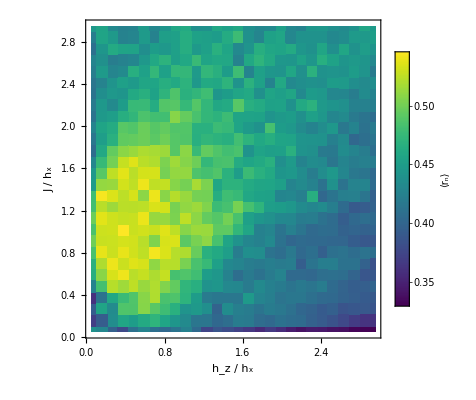

```mathematica
x=0.1;
r=Table[Join[points2[[i]],{MeanLevelSpacingRatio[eigenvalues[[i,2,Ceiling[1056*x];;Ceiling[1056*(1-x)]]]]}],{i,784}];
fontSize=18;
fig=
ListDensityPlot[r,
InterpolationOrder->0,
ColorFunction->(ResourceFunction["ViridisColor"][#]&),ColorFunctionScaling->True,
PlotLegends->Placed[BarLegend[Automatic,LegendLabel->"⟨r_n⟩",LabelStyle->Directive[FontFamily->"Arial",FontSize->fontSize,Black]],Automatic],
Frame->True,
FrameStyle->Directive[FontFamily->"Arial",FontSize->fontSize,Black],
FrameLabel->{"h_z / h_x","J / h_x"},
AspectRatio->1
]
```

```mathematica
filename="figs_ja/mean_level_spacing_ratio/wisniacki_open_L_11_hx_1_positive_parity_2.pdf";
Export[filename,fig,"PDF",ImageResolution->300]
RunProcess[{"pdfcrop",filename,filename}]
```

figs_ja/mean_level_spacing_ratio/wisniacki_open_L_11_hx_1_positive_parity_2.pdf

<|ExitCode→0,StandardOutput→PDFCROP 1.42, 2023/04/15 - Copyright (c) 2002-2023 by Heiko Oberdiek, Oberdiek Package Support Group.
==> 1 page written on `figs_ja/mean_level_spacing_ratio/wisniacki_open_L_11_hx_1_positive_parity_2.pdf'.
,StandardError→|>

```mathematica
Subdivide[0.05,2.95,29]
```

30

```mathematica
Tuples[Join[Flatten[Table[Subdivide[#[[i]],#[[i+1]],3][[1;;3]],{i,9}]],{2.95}],2]&[Subdivide[0.05,2.95,9]]
```

{{0.05,0.05},{0.05,0.157407},{0.05,0.264815},{0.05,0.372222},{0.05,0.47963},{0.05,0.587037},{0.05,0.694444},{0.05,0.801852},{0.05,0.909259},{0.05,1.01667},{0.05,1.12407},{0.05,1.23148},{0.05,1.33889},{0.05,1.4463},{0.05,1.5537},{0.05,1.66111},{0.05,1.76852},{0.05,1.87593},{0.05,1.98333},{0.05,2.09074},{0.05,2.19815},{0.05,2.30556},{0.05,2.41296},{0.05,2.52037},{0.05,2.62778},{0.05,2.73519},{0.05,2.84259},{0.05,2.95},{0.157407,0.05},{0.157407,0.157407},{0.157407,0.264815},{0.157407,0.372222},{0.157407,0.47963},{0.157407,0.587037},{0.157407,0.694444},{0.157407,0.801852},{0.157407,0.909259},{0.157407,1.01667},{0.157407,1.12407},{0.157407,1.23148},{0.157407,1.33889},{0.157407,1.4463},{0.157407,1.5537},{0.157407,1.66111},{0.157407,1.76852},{0.157407,1.87593},{0.157407,1.98333},{0.157407,2.09074},{0.157407,2.19815},{0.157407,2.30556},{0.157407,2.41296},{0.157407,2.52037},{0.157407,2.62778},{0.157407,2.73519},{0.157407,2.84259},{0.157407,2.95},{0.264815,0.05},{0.264815,0.157407},{0.264815,0.264815},{0.264815,0.372222},{0.264815,0.47963},{0.264815,0.587037},{0.264815,0.694444},{0.264815,0.801852},{0.264815,0.909259},{0.264815,1.01667},{0.264815,1.12407},{0.264815,1.23148},{0.264815,1.33889},{0.264815,1.4463},{0.264815,1.5537},{0.264815,1.66111},{0.264815,1.76852},{0.264815,1.87593},{0.264815,1.98333},{0.264815,2.09074},{0.264815,2.19815},{0.264815,2.30556},{0.264815,2.41296},{0.264815,2.52037},{0.264815,2.62778},{0.264815,2.73519},{0.264815,2.84259},{0.264815,2.95},{0.372222,0.05},{0.372222,0.157407},{0.372222,0.264815},{0.372222,0.372222},{0.372222,0.47963},{0.372222,0.587037},{0.372222,0.694444},{0.372222,0.801852},{0.372222,0.909259},{0.372222,1.01667},{0.372222,1.12407},{0.372222,1.23148},{0.372222,1.33889},{0.372222,1.4463},{0.372222,1.5537},{0.372222,1.66111},{0.372222,1.76852},{0.372222,1.87593},{0.372222,1.98333},{0.372222,2.09074},{0.372222,2.19815},{0.372222,2.30556},{0.372222,2.41296},{0.372222,2.52037},{0.372222,2.62778},{0.372222,2.73519},{0.372222,2.84259},{0.372222,2.95},{0.47963,0.05},{0.47963,0.157407},{0.47963,0.264815},{0.47963,0.372222},{0.47963,0.47963},{0.47963,0.587037},{0.47963,0.694444},{0.47963,0.801852},{0.47963,0.909259},{0.47963,1.01667},{0.47963,1.12407},{0.47963,1.23148},{0.47963,1.33889},{0.47963,1.4463},{0.47963,1.5537},{0.47963,1.66111},{0.47963,1.76852},{0.47963,1.87593},{0.47963,1.98333},{0.47963,2.09074},{0.47963,2.19815},{0.47963,2.30556},{0.47963,2.41296},{0.47963,2.52037},{0.47963,2.62778},{0.47963,2.73519},{0.47963,2.84259},{0.47963,2.95},{0.587037,0.05},{0.587037,0.157407},{0.587037,0.264815},{0.587037,0.372222},{0.587037,0.47963},{0.587037,0.587037},{0.587037,0.694444},{0.587037,0.801852},{0.587037,0.909259},{0.587037,1.01667},{0.587037,1.12407},{0.587037,1.23148},{0.587037,1.33889},{0.587037,1.4463},{0.587037,1.5537},{0.587037,1.66111},{0.587037,1.76852},{0.587037,1.87593},{0.587037,1.98333},{0.587037,2.09074},{0.587037,2.19815},{0.587037,2.30556},{0.587037,2.41296},{0.587037,2.52037},{0.587037,2.62778},{0.587037,2.73519},{0.587037,2.84259},{0.587037,2.95},{0.694444,0.05},{0.694444,0.157407},{0.694444,0.264815},{0.694444,0.372222},{0.694444,0.47963},{0.694444,0.587037},{0.694444,0.694444},{0.694444,0.801852},{0.694444,0.909259},{0.694444,1.01667},{0.694444,1.12407},{0.694444,1.23148},{0.694444,1.33889},{0.694444,1.4463},{0.694444,1.5537},{0.694444,1.66111},{0.694444,1.76852},{0.694444,1.87593},{0.694444,1.98333},{0.694444,2.09074},{0.694444,2.19815},{0.694444,2.30556},{0.694444,2.41296},{0.694444,2.52037},{0.694444,2.62778},{0.694444,2.73519},{0.694444,2.84259},{0.694444,2.95},{0.801852,0.05},{0.801852,0.157407},{0.801852,0.264815},{0.801852,0.372222},{0.801852,0.47963},{0.801852,0.587037},{0.801852,0.694444},{0.801852,0.801852},{0.801852,0.909259},{0.801852,1.01667},{0.801852,1.12407},{0.801852,1.23148},{0.801852,1.33889},{0.801852,1.4463},{0.801852,1.5537},{0.801852,1.66111},{0.801852,1.76852},{0.801852,1.87593},{0.801852,1.98333},{0.801852,2.09074},{0.801852,2.19815},{0.801852,2.30556},{0.801852,2.41296},{0.801852,2.52037},{0.801852,2.62778},{0.801852,2.73519},{0.801852,2.84259},{0.801852,2.95},{0.909259,0.05},{0.909259,0.157407},{0.909259,0.264815},{0.909259,0.372222},{0.909259,0.47963},{0.909259,0.587037},{0.909259,0.694444},{0.909259,0.801852},{0.909259,0.909259},{0.909259,1.01667},{0.909259,1.12407},{0.909259,1.23148},{0.909259,1.33889},{0.909259,1.4463},{0.909259,1.5537},{0.909259,1.66111},{0.909259,1.76852},{0.909259,1.87593},{0.909259,1.98333},{0.909259,2.09074},{0.909259,2.19815},{0.909259,2.30556},{0.909259,2.41296},{0.909259,2.52037},{0.909259,2.62778},{0.909259,2.73519},{0.909259,2.84259},{0.909259,2.95},{1.01667,0.05},{1.01667,0.157407},{1.01667,0.264815},{1.01667,0.372222},{1.01667,0.47963},{1.01667,0.587037},{1.01667,0.694444},{1.01667,0.801852},{1.01667,0.909259},{1.01667,1.01667},{1.01667,1.12407},{1.01667,1.23148},{1.01667,1.33889},{1.01667,1.4463},{1.01667,1.5537},{1.01667,1.66111},{1.01667,1.76852},{1.01667,1.87593},{1.01667,1.98333},{1.01667,2.09074},{1.01667,2.19815},{1.01667,2.30556},{1.01667,2.41296},{1.01667,2.52037},{1.01667,2.62778},{1.01667,2.73519},{1.01667,2.84259},{1.01667,2.95},{1.12407,0.05},{1.12407,0.157407},{1.12407,0.264815},{1.12407,0.372222},{1.12407,0.47963},{1.12407,0.587037},{1.12407,0.694444},{1.12407,0.801852},{1.12407,0.909259},{1.12407,1.01667},{1.12407,1.12407},{1.12407,1.23148},{1.12407,1.33889},{1.12407,1.4463},{1.12407,1.5537},{1.12407,1.66111},{1.12407,1.76852},{1.12407,1.87593},{1.12407,1.98333},{1.12407,2.09074},{1.12407,2.19815},{1.12407,2.30556},{1.12407,2.41296},{1.12407,2.52037},{1.12407,2.62778},{1.12407,2.73519},{1.12407,2.84259},{1.12407,2.95},{1.23148,0.05},{1.23148,0.157407},{1.23148,0.264815},{1.23148,0.372222},{1.23148,0.47963},{1.23148,0.587037},{1.23148,0.694444},{1.23148,0.801852},{1.23148,0.909259},{1.23148,1.01667},{1.23148,1.12407},{1.23148,1.23148},{1.23148,1.33889},{1.23148,1.4463},{1.23148,1.5537},{1.23148,1.66111},{1.23148,1.76852},{1.23148,1.87593},{1.23148,1.98333},{1.23148,2.09074},{1.23148,2.19815},{1.23148,2.30556},{1.23148,2.41296},{1.23148,2.52037},{1.23148,2.62778},{1.23148,2.73519},{1.23148,2.84259},{1.23148,2.95},{1.33889,0.05},{1.33889,0.157407},{1.33889,0.264815},{1.33889,0.372222},{1.33889,0.47963},{1.33889,0.587037},{1.33889,0.694444},{1.33889,0.801852},{1.33889,0.909259},{1.33889,1.01667},{1.33889,1.12407},{1.33889,1.23148},{1.33889,1.33889},{1.33889,1.4463},{1.33889,1.5537},{1.33889,1.66111},{1.33889,1.76852},{1.33889,1.87593},{1.33889,1.98333},{1.33889,2.09074},{1.33889,2.19815},{1.33889,2.30556},{1.33889,2.41296},{1.33889,2.52037},{1.33889,2.62778},{1.33889,2.73519},{1.33889,2.84259},{1.33889,2.95},{1.4463,0.05},{1.4463,0.157407},{1.4463,0.264815},{1.4463,0.372222},{1.4463,0.47963},{1.4463,0.587037},{1.4463,0.694444},{1.4463,0.801852},{1.4463,0.909259},{1.4463,1.01667},{1.4463,1.12407},{1.4463,1.23148},{1.4463,1.33889},{1.4463,1.4463},{1.4463,1.5537},{1.4463,1.66111},{1.4463,1.76852},{1.4463,1.87593},{1.4463,1.98333},{1.4463,2.09074},{1.4463,2.19815},{1.4463,2.30556},{1.4463,2.41296},{1.4463,2.52037},{1.4463,2.62778},{1.4463,2.73519},{1.4463,2.84259},{1.4463,2.95},{1.5537,0.05},{1.5537,0.157407},{1.5537,0.264815},{1.5537,0.372222},{1.5537,0.47963},{1.5537,0.587037},{1.5537,0.694444},{1.5537,0.801852},{1.5537,0.909259},{1.5537,1.01667},{1.5537,1.12407},{1.5537,1.23148},{1.5537,1.33889},{1.5537,1.4463},{1.5537,1.5537},{1.5537,1.66111},{1.5537,1.76852},{1.5537,1.87593},{1.5537,1.98333},{1.5537,2.09074},{1.5537,2.19815},{1.5537,2.30556},{1.5537,2.41296},{1.5537,2.52037},{1.5537,2.62778},{1.5537,2.73519},{1.5537,2.84259},{1.5537,2.95},{1.66111,0.05},{1.66111,0.157407},{1.66111,0.264815},{1.66111,0.372222},{1.66111,0.47963},{1.66111,0.587037},{1.66111,0.694444},{1.66111,0.801852},{1.66111,0.909259},{1.66111,1.01667},{1.66111,1.12407},{1.66111,1.23148},{1.66111,1.33889},{1.66111,1.4463},{1.66111,1.5537},{1.66111,1.66111},{1.66111,1.76852},{1.66111,1.87593},{1.66111,1.98333},{1.66111,2.09074},{1.66111,2.19815},{1.66111,2.30556},{1.66111,2.41296},{1.66111,2.52037},{1.66111,2.62778},{1.66111,2.73519},{1.66111,2.84259},{1.66111,2.95},{1.76852,0.05},{1.76852,0.157407},{1.76852,0.264815},{1.76852,0.372222},{1.76852,0.47963},{1.76852,0.587037},{1.76852,0.694444},{1.76852,0.801852},{1.76852,0.909259},{1.76852,1.01667},{1.76852,1.12407},{1.76852,1.23148},{1.76852,1.33889},{1.76852,1.4463},{1.76852,1.5537},{1.76852,1.66111},{1.76852,1.76852},{1.76852,1.87593},{1.76852,1.98333},{1.76852,2.09074},{1.76852,2.19815},{1.76852,2.30556},{1.76852,2.41296},{1.76852,2.52037},{1.76852,2.62778},{1.76852,2.73519},{1.76852,2.84259},{1.76852,2.95},{1.87593,0.05},{1.87593,0.157407},{1.87593,0.264815},{1.87593,0.372222},{1.87593,0.47963},{1.87593,0.587037},{1.87593,0.694444},{1.87593,0.801852},{1.87593,0.909259},{1.87593,1.01667},{1.87593,1.12407},{1.87593,1.23148},{1.87593,1.33889},{1.87593,1.4463},{1.87593,1.5537},{1.87593,1.66111},{1.87593,1.76852},{1.87593,1.87593},{1.87593,1.98333},{1.87593,2.09074},{1.87593,2.19815},{1.87593,2.30556},{1.87593,2.41296},{1.87593,2.52037},{1.87593,2.62778},{1.87593,2.73519},{1.87593,2.84259},{1.87593,2.95},{1.98333,0.05},{1.98333,0.157407},{1.98333,0.264815},{1.98333,0.372222},{1.98333,0.47963},{1.98333,0.587037},{1.98333,0.694444},{1.98333,0.801852},{1.98333,0.909259},{1.98333,1.01667},{1.98333,1.12407},{1.98333,1.23148},{1.98333,1.33889},{1.98333,1.4463},{1.98333,1.5537},{1.98333,1.66111},{1.98333,1.76852},{1.98333,1.87593},{1.98333,1.98333},{1.98333,2.09074},{1.98333,2.19815},{1.98333,2.30556},{1.98333,2.41296},{1.98333,2.52037},{1.98333,2.62778},{1.98333,2.73519},{1.98333,2.84259},{1.98333,2.95},{2.09074,0.05},{2.09074,0.157407},{2.09074,0.264815},{2.09074,0.372222},{2.09074,0.47963},{2.09074,0.587037},{2.09074,0.694444},{2.09074,0.801852},{2.09074,0.909259},{2.09074,1.01667},{2.09074,1.12407},{2.09074,1.23148},{2.09074,1.33889},{2.09074,1.4463},{2.09074,1.5537},{2.09074,1.66111},{2.09074,1.76852},{2.09074,1.87593},{2.09074,1.98333},{2.09074,2.09074},{2.09074,2.19815},{2.09074,2.30556},{2.09074,2.41296},{2.09074,2.52037},{2.09074,2.62778},{2.09074,2.73519},{2.09074,2.84259},{2.09074,2.95},{2.19815,0.05},{2.19815,0.157407},{2.19815,0.264815},{2.19815,0.372222},{2.19815,0.47963},{2.19815,0.587037},{2.19815,0.694444},{2.19815,0.801852},{2.19815,0.909259},{2.19815,1.01667},{2.19815,1.12407},{2.19815,1.23148},{2.19815,1.33889},{2.19815,1.4463},{2.19815,1.5537},{2.19815,1.66111},{2.19815,1.76852},{2.19815,1.87593},{2.19815,1.98333},{2.19815,2.09074},{2.19815,2.19815},{2.19815,2.30556},{2.19815,2.41296},{2.19815,2.52037},{2.19815,2.62778},{2.19815,2.73519},{2.19815,2.84259},{2.19815,2.95},{2.30556,0.05},{2.30556,0.157407},{2.30556,0.264815},{2.30556,0.372222},{2.30556,0.47963},{2.30556,0.587037},{2.30556,0.694444},{2.30556,0.801852},{2.30556,0.909259},{2.30556,1.01667},{2.30556,1.12407},{2.30556,1.23148},{2.30556,1.33889},{2.30556,1.4463},{2.30556,1.5537},{2.30556,1.66111},{2.30556,1.76852},{2.30556,1.87593},{2.30556,1.98333},{2.30556,2.09074},{2.30556,2.19815},{2.30556,2.30556},{2.30556,2.41296},{2.30556,2.52037},{2.30556,2.62778},{2.30556,2.73519},{2.30556,2.84259},{2.30556,2.95},{2.41296,0.05},{2.41296,0.157407},{2.41296,0.264815},{2.41296,0.372222},{2.41296,0.47963},{2.41296,0.587037},{2.41296,0.694444},{2.41296,0.801852},{2.41296,0.909259},{2.41296,1.01667},{2.41296,1.12407},{2.41296,1.23148},{2.41296,1.33889},{2.41296,1.4463},{2.41296,1.5537},{2.41296,1.66111},{2.41296,1.76852},{2.41296,1.87593},{2.41296,1.98333},{2.41296,2.09074},{2.41296,2.19815},{2.41296,2.30556},{2.41296,2.41296},{2.41296,2.52037},{2.41296,2.62778},{2.41296,2.73519},{2.41296,2.84259},{2.41296,2.95},{2.52037,0.05},{2.52037,0.157407},{2.52037,0.264815},{2.52037,0.372222},{2.52037,0.47963},{2.52037,0.587037},{2.52037,0.694444},{2.52037,0.801852},{2.52037,0.909259},{2.52037,1.01667},{2.52037,1.12407},{2.52037,1.23148},{2.52037,1.33889},{2.52037,1.4463},{2.52037,1.5537},{2.52037,1.66111},{2.52037,1.76852},{2.52037,1.87593},{2.52037,1.98333},{2.52037,2.09074},{2.52037,2.19815},{2.52037,2.30556},{2.52037,2.41296},{2.52037,2.52037},{2.52037,2.62778},{2.52037,2.73519},{2.52037,2.84259},{2.52037,2.95},{2.62778,0.05},{2.62778,0.157407},{2.62778,0.264815},{2.62778,0.372222},{2.62778,0.47963},{2.62778,0.587037},{2.62778,0.694444},{2.62778,0.801852},{2.62778,0.909259},{2.62778,1.01667},{2.62778,1.12407},{2.62778,1.23148},{2.62778,1.33889},{2.62778,1.4463},{2.62778,1.5537},{2.62778,1.66111},{2.62778,1.76852},{2.62778,1.87593},{2.62778,1.98333},{2.62778,2.09074},{2.62778,2.19815},{2.62778,2.30556},{2.62778,2.41296},{2.62778,2.52037},{2.62778,2.62778},{2.62778,2.73519},{2.62778,2.84259},{2.62778,2.95},{2.73519,0.05},{2.73519,0.157407},{2.73519,0.264815},{2.73519,0.372222},{2.73519,0.47963},{2.73519,0.587037},{2.73519,0.694444},{2.73519,0.801852},{2.73519,0.909259},{2.73519,1.01667},{2.73519,1.12407},{2.73519,1.23148},{2.73519,1.33889},{2.73519,1.4463},{2.73519,1.5537},{2.73519,1.66111},{2.73519,1.76852},{2.73519,1.87593},{2.73519,1.98333},{2.73519,2.09074},{2.73519,2.19815},{2.73519,2.30556},{2.73519,2.41296},{2.73519,2.52037},{2.73519,2.62778},{2.73519,2.73519},{2.73519,2.84259},{2.73519,2.95},{2.84259,0.05},{2.84259,0.157407},{2.84259,0.264815},{2.84259,0.372222},{2.84259,0.47963},{2.84259,0.587037},{2.84259,0.694444},{2.84259,0.801852},{2.84259,0.909259},{2.84259,1.01667},{2.84259,1.12407},{2.84259,1.23148},{2.84259,1.33889},{2.84259,1.4463},{2.84259,1.5537},{2.84259,1.66111},{2.84259,1.76852},{2.84259,1.87593},{2.84259,1.98333},{2.84259,2.09074},{2.84259,2.19815},{2.84259,2.30556},{2.84259,2.41296},{2.84259,2.52037},{2.84259,2.62778},{2.84259,2.73519},{2.84259,2.84259},{2.84259,2.95},{2.95,0.05},{2.95,0.157407},{2.95,0.264815},{2.95,0.372222},{2.95,0.47963},{2.95,0.587037},{2.95,0.694444},{2.95,0.801852},{2.95,0.909259},{2.95,1.01667},{2.95,1.12407},{2.95,1.23148},{2.95,1.33889},{2.95,1.4463},{2.95,1.5537},{2.95,1.66111},{2.95,1.76852},{2.95,1.87593},{2.95,1.98333},{2.95,2.09074},{2.95,2.19815},{2.95,2.30556},{2.95,2.41296},{2.95,2.52037},{2.95,2.62778},{2.95,2.73519},{2.95,2.84259},{2.95,2.95}}